寻找比 Stirling公式n!≈(n/ⅇ)^n √(2 π n)更精细的近似公式。

```mathematica
Limit[n^2*(n!/((n^n*Exp[-n]*Sqrt[n]*(1+1/(12n))))-Sqrt[2Pi]),n->Infinity]
```

(√(π/2))/144

```mathematica
Clear[string,newformula1,newformula2,n];string=n!/(n^n*Exp[-n]*Sqrt[n]);
lim=Limit[string,n->Infinity]
newformula1=(string-Sqrt[2Pi])n;
lim=Limit[newformula1,n->Infinity]
newformula2=(newformula1-lim )n;
lim=Limit[newformula2,n->Infinity]
```

√(2 π)

(√(π/2))/6

(√(π/2))/144

```mathematica
newformula2=(newformula2-lim )n;
lim=Limit[newformula2,n->Infinity]
```

-(139 √(π/2))/25920

```mathematica
newformula2
```

n (-(√(π/2))/144+n (-(√(π/2))/6+n (-√(2 π)+ⅇ^n n^(-1/2-n) n!)))

```mathematica
Limit[newformula2,n->Infinity]
```

-(139 √(π/2))/25920

设递推数列 x_1∈(0,1),x_(n+1)=x_n-x_n^k。求其收敛速度。

```mathematica
new=0;(*SeedRandom[IntegerPart[AbsoluteTime[]]]*)
For[j=1,j<11,j++,x1=0.1(*RandomReal[]*);k=3;speed=1;n=700000;x=x1;
For[i=1,i<n,i++,y=x-x^k;speed=speed*y/x;x=y(*Print[x,"    speed    ",speed]*)];new=new-Log[speed];];new
```

47.7345

```mathematica
100000,38.0072
200000,41.4716
300000,43.4985
400000,44.9367
500000,46.0523
600000    46.9637
700000   47.7345
```

```mathematica
data={{100000,38.0072},{200000,41.4716},{300000,43.4985},{400000,44.9367},{500000,46.0523},{600000,46.9637}}
```

{{100000,38.0072},{200000,41.4716},{300000,43.4985},{400000,44.9367},{500000,46.0523},{600000,46.9637}}

{38.0072,41.4716,43.4985,44.9367,46.0523,46.9637,47.7345}

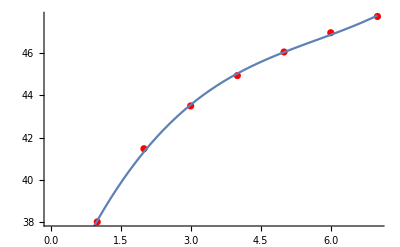

33.4977+5.31594 x-0.79488 x^2+0.0467056 x^3

```mathematica
v={38.0072,41.4716,43.4985,44.9367,46.0523,46.9637,47.7345}
Clear[x];parabola=Fit[v, {1,x,x^2,x^3}, x];Show[ListPlot[v, PlotStyle->Red], Plot[{ parabola}, {x, 0,7}]]
parabola
```

设计更好的方法计算 ln10，精确到10^-10。

```mathematica
Log[10]
```

```mathematica
Integrate[1/x,{x,1,10}]
```

```mathematica
Log[2]
```

```mathematica
N[Log[10]]
```

2.30259

```mathematica
Integrate[1/x,{x,8,10}]
```

Log[5/4]

```mathematica
N[Log[5/4]]
```

0.223144

```mathematica
s=1000000;N[Sum[1/n,{n,8s/10,s}]]
```

0.223145

```mathematica
Log[10]=8Log[Sqrt[Sqrt[Sqrt[10]]]]
```

10^(1/8)

```mathematica
N[10^(1/8),12]
```

1.33352143216

```mathematica
N[8*Log[1-0.33352143216/1.33352143216]+Log[10]]
```

1.99414×10^-11

```mathematica
0.33352143216/1.33352143216
```

0.250106

```mathematica
8*0.25^17/17
```

2.73918×10^-11

设计更好的方法计算 cos1，精确到10^-10。

```mathematica
1-1/(1*2+(1*2)/(3*4-1+(3*4)/(5*6-1+5*6/(7*8))))
```

11087/20520

```mathematica
N[11087/20520]
```

0.540302

```mathematica
N[Cos[1]]
```

0.540302

加速数列 x_n=∏_(k=1)^n (1-1/(4 n^2))→2/π 的收敛。

```mathematica
Sum[Log[1-1/(4n^2)],{n,1,Infinity}]
```

Log[2]-Log[π]

```mathematica
N[Log[2]-Log[π]]
```

-0.451583

```mathematica
Clear[n];
Series[a/n+b/n^2+c/n^3+d/n^4-a/(n+1)-b/(n+1)^2-c/(n+1)^3-d/(n+1)^4-Log[1-1/(4n^2)],{n,Infinity,8}]
```

(1/4+a)/n^2+(-a+2 b)/n^3+(1/32+a-3 b+3 c)/n^4+(-a+4 b-6 c+4 d)/n^5+(1/192+a-5 b+10 c-10 d)/n^6+(-a+6 b-15 c+20 d)/n^7+(1/1024+a-7 b+21 c-35 d)/n^8+O[1/n]^9

```mathematica
Solve[{1/4+a==0,-a+2 b==0,1/32+a-3 b+3 c==0,-a+4 b-6 c+4 d==0},{a,b,c,d}]
```

{{a→-1/4,b→-1/8,c→-5/96,d→-1/64}}

```mathematica
(1/192+a-5 b+10 c-10 d)/n^6+(-a+6 b-15 c+20 d)/n^7+(1/1024+a-7 b+21 c-35 d)/n^8/.%
```

{81/(1024 n^8)-1/(32 n^7)+1/(64 n^6)}

```mathematica
n=24;N[1/(320 n^5)]
```

3.92459×10^-10

```mathematica
n=3000;N[Sum[Log[1-1/(4m^2)],{m,1,n}]]-(1/(4n)+1/(8 n^2)+5/(96 n^3)+1/(64 n^4)-1/(320 n^5))-Log[2]+Log[π]
```

-2.77778×10^-8

```mathematica
N[Sum[Log[1-1/(4n^2)],{n,1,700000}]]-Log[2]+Log[π]
```

3.57143×10^-7

这里很奇怪的是修正后的收敛行为并没有遵循O[1/(320 n^5)],一个自然的想法是log的展开的行为和例题中的8/((4k+1)(4k+3))不太一样，但是这种方法确实也加速了收敛。